```mathematica
contourRegionPlot3D[region_,{x_,x0_,x1_},{y_,y0_,y1_},{z_,z0_,z1_},opts:OptionsPattern[]]:=Module[{reg,preds},reg=LogicalExpand[region&&x0≤x≤x1&&y0≤y≤y1&&z0≤z≤z1];
preds=Union@Cases[reg,_Greater|_GreaterEqual|_Less|_LessEqual,-1];
Show@Table[ContourPlot3D[Evaluate[Equal@@p],{x,x0,x1},{y,y0,y1},{z,z0,z1},RegionFunction->Function@@{{x,y,z},Refine[reg,p]&&Refine[!reg,!p]},opts],{p,preds}]]
```

```mathematica
R = contourRegionPlot3D[2*x1-x2+x3 ≥ -1 && x1+2*x3≥2 && -7*x1+4*x2-6*x3≥1,{x1,-2,20},{x2,0,80},{x3,-10,10},PlotPoints->80,Mesh->None,ContourStyle->Directive[Red,Opacity[0.4],Specularity[White,30]]]
```

-Graphics3D-

```mathematica
H = Graphics3D[{Blue,Opacity[0.5],Hyperplane[{3,-1,2},{0,0,0}]}]
```

-Graphics3D-

```mathematica
Show[R,H]
```

-Graphics3D-

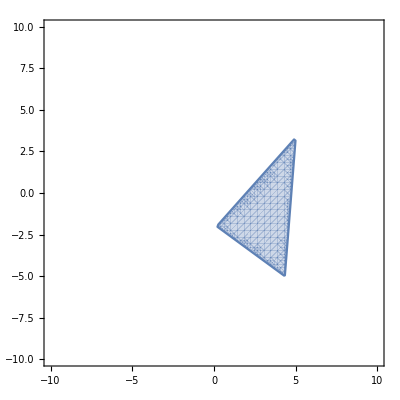

```mathematica
RegionPlot[96*x-87*y>=190 && 18*x+25*y ≥ -47 && -75*x+6*y≥ -355,{x,-10,10},{y,-10,10},PlotPoints->50]
```